```mathematica
(*ClearAll["Global`*"]*)
ClearAll["Global`*"]

(* Table format R,E, E + 1/R,A,p *)
gerade =Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx"];
```

```mathematica
Dimensions[gerade]
```

```mathematica
(* R -> V(R) *)
geradePotential=Table[{gerade[[i,1]],gerade[[i,3]]},{i,1,27}]
```

{{0.2,-1.50328},{0.3,-2.48639},{0.4,-2.77548},{0.5,-2.8382},{0.6,-2.81481},{0.7,-2.75759},{0.8,-2.68852},{0.9,-2.61749},{1.,-2.54904},{1.1,-2.4852},{1.5,-2.28416},{2.,-2.13638},{2.5,-2.0621},{3.,-2.02753},{3.5,-2.01226},{4.,-2.00568},{4.5,-2.00284},{5.,-2.00156},{6,-2.00065},{7,-2.00036},{8,-2.00023},{9,-2.00016},{10,-2.00012},{11,-2.00009},{12,-2.00006},{13,-2.00004},{14,-2.00001}}

```mathematica
(* Long range behaviour *)
long[R_]=-2.0-0.082/R^4
```

-2.-0.082/R^4

```mathematica
geradefun=Interpolation[geradePotential]
```

InterpolatingFunction[…]

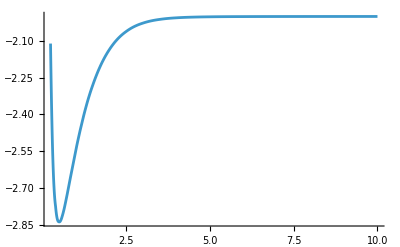

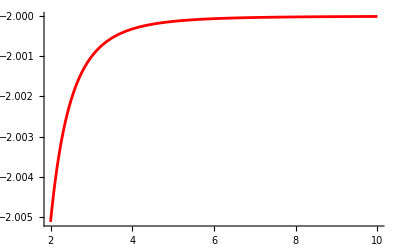

```mathematica
(* Plot of the 1S potential curve (g1) and the long range behaviour (g2) *)
g1=Plot[geradefun[R],{R,0.25,10},PlotRange->All]
g2=Plot[long[R],{R,2,10},PlotRange->All,PlotStyle->Red]
```

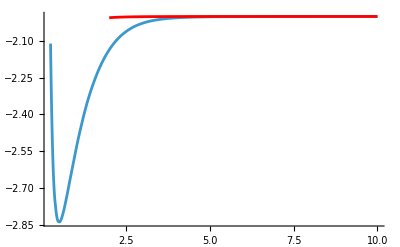

```mathematica
(* Comparison between g1 and g2 *)
Show[g1,g2]
```

```mathematica
(* Fit to a model *)
gdata=Drop[geradePotential,{5,27}]
model[R_,C1_,C2_,C3_]:=C1 Exp[-C2 R]/R+C3
```

```mathematica
gnlm=NonlinearModelFit[gdata,model[R,C1,C2,C3],{C1,C2,C3},R]
```

FittedModel[…]

```mathematica
gnlm["BestFitParameters"]
```

{C1→1.49799,C2→8.42799,C3→-2.89071}

```mathematica
gshort[R_]=model[R,C1,C2,C3] /. gnlm["BestFitParameters"]
```

-2.89071+(1.49799 ⅇ^(-8.42799 R))/R

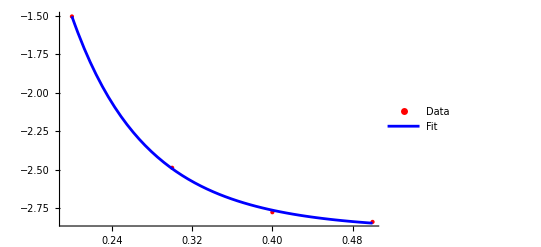

```mathematica
Show[ListPlot[gdata,PlotStyle->{Red,PointSize[Medium]},PlotLegends->{"Data"}],Plot[gnlm[R],{R,Min[gdata[[All,1]]],Max[gdata[[All,1]]]},PlotStyle->Blue,PlotLegends->{"Fit"}]]
```

```mathematica
gpot[R_]=Piecewise[{{gshort[R],R<=0.3},{geradefun[R],0.3<R<13.0},{long[R],R>=13.0}}]
```

Piecewise[{{-2.89071+(1.49799 ⅇ^(-8.42799 R))/R, R≤0.3}, {InterpolatingFunction[…][R], 0.3<R<13.}, {-2.-0.082/R^4, R≥13.}, {0, True}}]

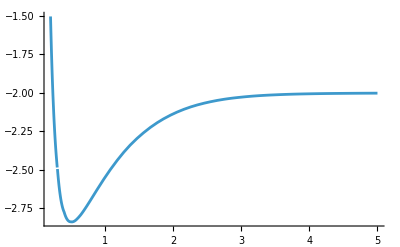

```mathematica
Plot[gpot[R],{R,0.2,5},PlotRange->All]
```

```mathematica
(*ClearAll["Global`*"]*)
(* Now same for the ungerade potential *)
ungerade = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx"];
```

```mathematica
ungeradePotential=Table[{ungerade[[i,1]],ungerade[[i,3]]},{i,1,27}]
```

{{0.2,4.15868},{0.3,2.42148},{0.4,1.46676},{0.5,0.798837},{0.6,0.273983},{0.7,-0.153558},{0.8,-0.502669},{0.9,-0.786143},{1.,-1.01521},{1.1,-1.1999},{1.5,-1.64494},{2.,-1.86744},{2.5,-1.95029},{3.,-1.98193},{3.5,-1.99399},{4.,-1.99845},{4.5,-2.},{5.,-2.00046},{6,-2.00049},{7,-2.00034},{8,-2.00023},{9,-2.00016},{10,-2.00012},{11,-2.00009},{12,-2.00007},{13,-2.00005},{14,-2.00004}}

```mathematica
long[R_]=-2.0-0.082/R^4
```

-2.-0.082/R^4

```mathematica
ungeradefun=Interpolation[ungeradePotential]
```

InterpolatingFunction[…]

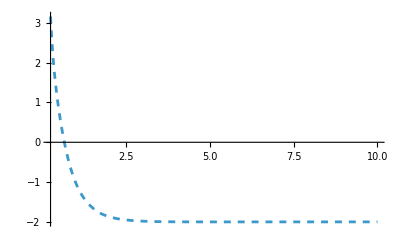

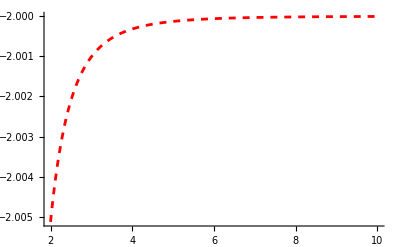

```mathematica
u1=Plot[ungeradefun[R],{R,0.25,10},PlotRange->All,PlotStyle->Dashed]
u2=Plot[long[R],{R,2,10},PlotRange->All,PlotStyle->{Red,Dashed}]
```

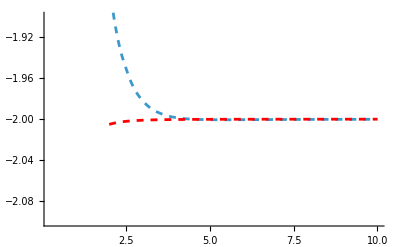

```mathematica
Show[u1,u2,PlotRange->{All,{-2.1,-1.9}}]
```

```mathematica
udata=Drop[myungerade,{5,27}]
model[R_,C1_,C2_,C3_]:=C1 /R+C3
```

{{0.2,4.15868},{0.3,2.42148},{0.4,1.46676},{0.5,0.798837}}

```mathematica
unlm=NonlinearModelFit[udata,model[R,C1,C2,C3],{C1,C2,C3},R]
```

FittedModel[…]

```mathematica
unlm["BestFitParameters"]
```

{C1→1.10832,C2→0.,C3→-1.34444}

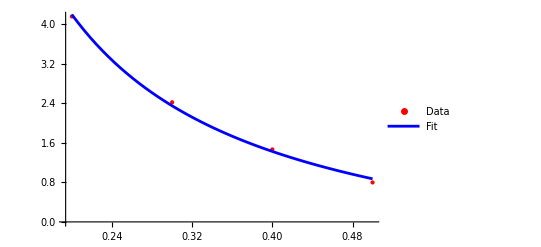

```mathematica
Show[ListPlot[udata,PlotStyle->{Red,PointSize[Medium]},PlotLegends->{"Data"}],Plot[unlm[R],{R,Min[udata[[All,1]]],Max[udata[[All,1]]]},PlotStyle->Blue,PlotLegends->{"Fit"}]]
```

```mathematica
ushort[R_]=model[R,C1,C2,C3] /. unlm["BestFitParameters"]
```

-1.34444+1.10832/R

```mathematica
upot[R_]=Piecewise[{{ushort[R],R<=0.3},{ungeradefun[R],0.3<R<13.0},{long[R],R>=13.0}}]
```

Piecewise[{{-1.34444+1.10832/R, R≤0.3}, {InterpolatingFunction[…][R], 0.3<R<13.}, {-2.-0.082/R^4, R≥13.}, {0, True}}]

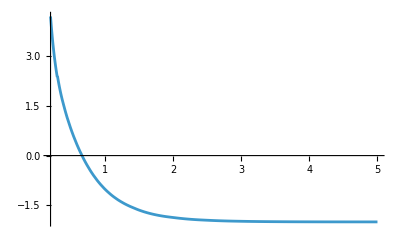

```mathematica
Plot[upot[R],{R,0.2,5},PlotRange->All]
```

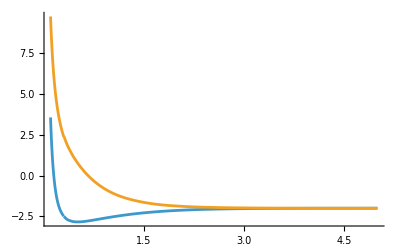

```mathematica
(* Potenial curves comparison  Gerade (gpot), ungerade (upot) *)
g1=Plot[{gpot[R],upot[R]},{R,0.1,5},PlotRange->All]
```

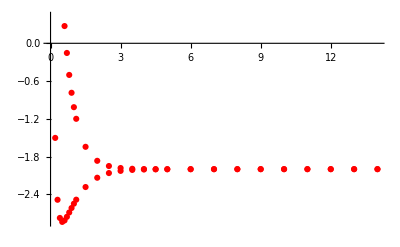

```mathematica
g2=ListPlot[{mygerade,myungerade},PlotStyle->Red]
```

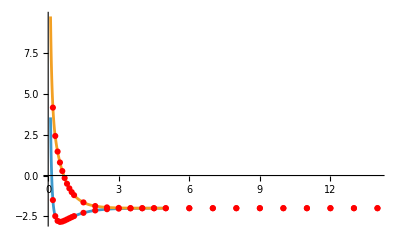

```mathematica
Show[g1,g2]
```